# Mechanism 11 analytical solution

```mathematica
Clear[th2,th3]
```

Here we input the first 3 position equations and their derivatives to get all the data related to theta 3 and the position of the slider.

```mathematica
positionequation1 = R2*Cos[th2]+R3*Cos[th3]-R4
```

-R4+R2 Cos[th2]+R3 Cos[th3]

```mathematica
velocityequation1=R2*Sin[th2]*omega2+R3*Sin[th3]*omega3+v4
```

v4+omega2 R2 Sin[th2]+omega3 R3 Sin[th3]

```mathematica
accelerationequation1=R2*Cos[th2]*(omega2)^2+R2*Sin[th2]*alpha2+R3*Cos[th3]*omega3^2+R3*Sin[th3]*alpha3+a4
```

a4+omega2^2 R2 Cos[th2]+omega3^2 R3 Cos[th3]+alpha2 R2 Sin[th2]+alpha3 R3 Sin[th3]

```mathematica
positionequation2 = R2*Sin[th2]+R3*Sin[th3]
```

R2 Sin[th2]+R3 Sin[th3]

```mathematica
velocityequation2=R2*Cos[th2]*omega2+R3*Cos[th3]*omega3
```

omega2 R2 Cos[th2]+omega3 R3 Cos[th3]

```mathematica
accelerationequation2=-R2*Sin[th2]*omega2^2+R2*Cos[th2]*alpha2-R3*Sin[th3]*omega3^2+R3*Cos[th3]*alpha3
```

alpha2 R2 Cos[th2]+alpha3 R3 Cos[th3]-omega2^2 R2 Sin[th2]-omega3^2 R3 Sin[th3]

Now we plug in the length of each side. R2 is AB,R3 is BC and it is assumed that link AB is rotating with constant speed of 1000 rpm ccw

```mathematica
R2 = 14
R3 = 41
omega2 = 1000*2*3.14/60
alpha2 = 0
```

14

41

104.667

0

Here we start plotting the data related to the previous equations.when solving the equations we have a system of non linear equations so it is obvious that we always have 2 solutions including one refused one. the plots shows the accepted answer.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

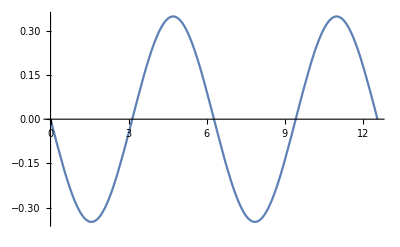

```mathematica
Plot[th3/.NSolve[{positionequation1==0,positionequation2==0},{th3,R4}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

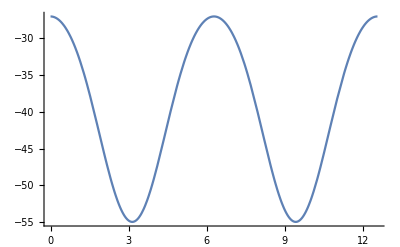

```mathematica
Plot[R4/.NSolve[{positionequation1==0,positionequation2==0},{th3,R4}][[1]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

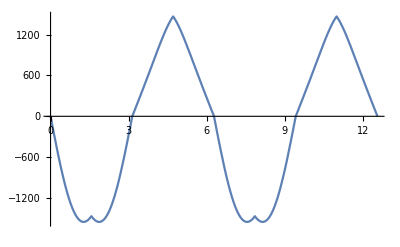

```mathematica
Plot[v4/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0},{th3,R4,v4,omega3}][[1]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

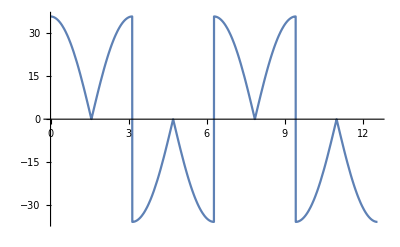

```mathematica
Plot[omega3/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0},{th3,R4,v4,omega3}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

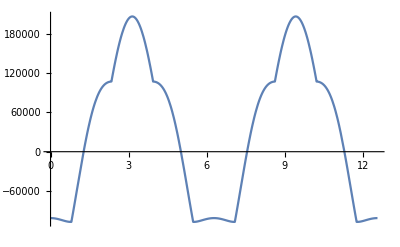

```mathematica
Plot[a4/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0,accelerationequation1==0,accelerationequation2==0},{th3,R4,v4,omega3,a4,alpha3}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

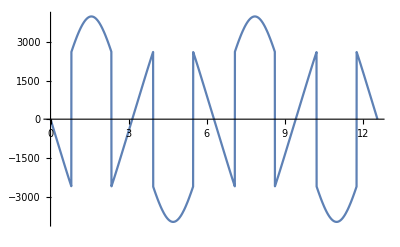

```mathematica
Plot[alpha3/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0,accelerationequation1==0,accelerationequation2==0},{th3,R4,v4,omega3,a4,alpha3}][[2]],{th2,0,4*Pi}]
```

Here we plug in the next required equations to get the data related to theta 5,theta 6. here we find that we used the link R31 which is equivalent to the side BD in the triangle. there relation between it’s angle and theta 3 is : theta31 = angle(DBC)-theta3 so angle DBC was evaluated using law of cosines and it is found in the equations.

```mathematica
positionequation3 = R2*Cos[th2]+R31*Cos[1.327102-th3]+R5*Cos[th5]+R6*Cos[th6]-A
```

7.63087-A+R31 Cos[1.3271-th3]+R5 Cos[th5]+R6 Cos[th6]

```mathematica
positionequation4=R2*Sin[th2]+R31*Sin[1.327102-th3]+R5*Sin[th5]+R6*Sin[th6]-B
```

11.7375-B+R31 Sin[1.3271-th3]+R5 Sin[th5]+R6 Sin[th6]

```mathematica
velocityequation3 = -R2*Sin[th2]*omega2+R31*Sin[1.327102-th3]*omega3-R5*Sin[th5]*omega5-R6*Sin[th6]*omega6
```

-1228.53+omega3 R31 Sin[1.3271-th3]-omega5 R5 Sin[th5]-omega6 R6 Sin[th6]

```mathematica
velocityequation4 = R2*Cos[th2]*omega2-R31*Cos[1.327102-th3]*omega3+R5*Cos[th5]*omega5+R6*Cos[th6]*omega6
```

798.697-omega3 R31 Cos[1.3271-th3]+omega5 R5 Cos[th5]+omega6 R6 Cos[th6]

```mathematica
accelerationequation3 = -R2*Cos[th2]*omega2^2-R2*Sin[th2]*alpha2-R31*Cos[1.327102-th3]*omega3^2+R31*Sin[1.327102-th3]*alpha3-R5*Cos[th5]*omega5^2-R5*Sin[th5]*alpha5-R6*Cos[th6]*omega6^2-R6*Sin[th6]*alpha6
```

-83597.-omega3^2 R31 Cos[1.3271-th3]-omega5^2 R5 Cos[th5]-omega6^2 R6 Cos[th6]+alpha3 R31 Sin[1.3271-th3]-alpha5 R5 Sin[th5]-alpha6 R6 Sin[th6]

```mathematica
accelerationequation4=-R2*Sin[th2]*omega2^2+R2*Cos[th2]*alpha2-R31*Sin[1.327102-th3]*omega3^2-R31*Cos[1.327102-th3]*alpha3-R5*Sin[th5]*omega5^2+R5*Cos[th5]*alpha5-R6*Sin[th6]*omega6^2+R6*Cos[th6]*alpha6
```

-128586.-alpha3 R31 Cos[1.3271-th3]+alpha5 R5 Cos[th5]+alpha6 R6 Cos[th6]-omega3^2 R31 Sin[1.3271-th3]-omega5^2 R5 Sin[th5]-omega6^2 R6 Sin[th6]

now again we introduce the required constants. the vector Ai+Bj is the same as the vector starting from point A to point F. It is a constant one and the values of A and B are measured using linkage program.

```mathematica
R5 = 63
R6 = 76
R31 = 14
A = 59.6
B = 24.457
```

63

76

14

59.6

24.457

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

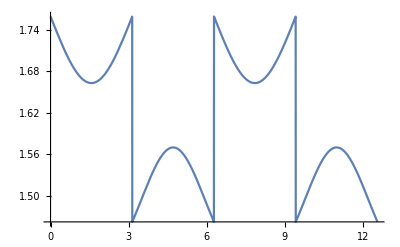

```mathematica
Plot[th5/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0},{th3,th5,th6}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

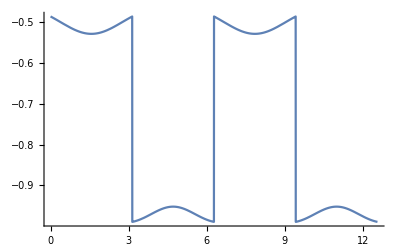

```mathematica
Plot[th6/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0},{th3,th5,th6}][[2]],{th2,0,4*Pi}]
```

```mathematica
Show[%90,AxesStyle->Black]
```

-Graphics-

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

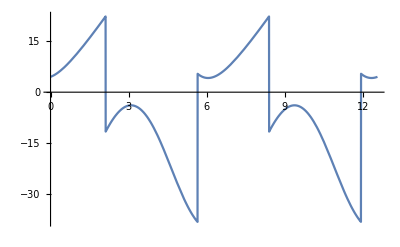

```mathematica
Plot[omega5/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0},{th3,th5,th6,omega5,omega6,omega3}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

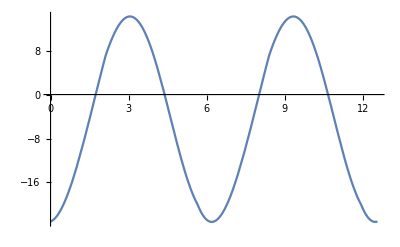

```mathematica
Plot[omega6/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0},{th3,th5,th6,omega5,omega6,omega3}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

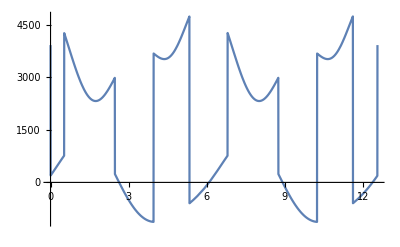

```mathematica
Plot[alpha5/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0,accelerationequation2==0,accelerationequation3==0,accelerationequation4==0},{th3,th5,th6,omega5,omega6,omega3,alpha3,alpha5,alpha6}][[2]],{th2,0,4*Pi}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

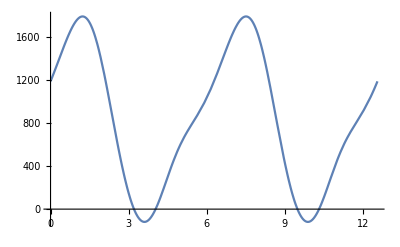

```mathematica
Plot[alpha6/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0,accelerationequation2==0,accelerationequation3==0,accelerationequation4==0},{th3,th5,th6,omega5,omega6,omega3,alpha3,alpha5,alpha6}][[1]],{th2,0,4*Pi}]
```

# Now let’s make sure that the graphs are right

As the mechanism was drawn. theta2=57 so the graphical solution is evaluated at this instant.

```mathematica
-Graphics--Graphics-
```

```mathematica
th2 = 57*3.14/180
v4/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0},{th3,R4,v4,omega3}][[1]]
```

0.994333

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-1467.17

```mathematica
omega3/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0},{th3,R4,v4,omega3}][[2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

20.3314

```mathematica
omega5/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0},{th3,th5,th6,omega5,omega6,omega3}][[2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

6.06847

```mathematica
omega6/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0},{th3,th5,th6,omega5,omega6,omega3}][[2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-18.4986

```mathematica
alpha3/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0,accelerationequation1==0,accelerationequation2==0},{th3,R4,v4,omega3,a4,alpha3}][[2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

3149.74

```mathematica
alpha5/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0,accelerationequation2==0,accelerationequation3==0,accelerationequation4==0},{th3,th5,th6,omega5,omega6,omega3,alpha3,alpha5,alpha6}][[2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

3572.4

```mathematica
alpha6/.NSolve[{positionequation2==0,positionequation3==0,positionequation4==0,velocityequation2==0,velocityequation3==0,velocityequation4==0,accelerationequation2==0,accelerationequation3==0,accelerationequation4==0},{th3,th5,th6,omega5,omega6,omega3,alpha3,alpha5,alpha6}][[1]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

1819.

```mathematica
a4/.NSolve[{positionequation1==0,positionequation2==0,velocityequation1==0,velocityequation2==0,accelerationequation1==0,accelerationequation2==0},{th3,R4,v4,omega3,a4,alpha3}][[2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-62865.5